# Kapitola 3 - Křížová validace Demonstrace použití křížové validace při klasifikování dat.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\BP

A načteme data.

```mathematica
data=Import["iris.data"];
```

### Načtení dat z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako při načítání ze souboru, jen načtena přímo z internetu.

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Příprava trénovacích dat

Provedeme předzpracování dat stejným postupem, jaký je popsán v kapitole Dopředná síť a Iris data.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];
outDataTmp=data2[[All,5]];
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

Data odsahují 4 vstupní parametry, podle kterých budeme klasifikovat do třech tříd.

## Křížová validace (Cross validation)

Nejprve si vytvoříme neuronovou síť, kterou budeme pomocí křížové validace vyhodnocovat.

```mathematica
net=InitializeFeedForwardNet[inData,outData,{3,2},Neuron->Sigmoid]
```

General::obspkg: "Histograms`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

FeedForwardNet[{{w1,w2,w3}},{Neuron → Sigmoid, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 5, 13, 14, 40, 28.5856321}, OutputNonlinearity → None, NumberOfInputs → 4}]

Můžeme si zobrazit informace o síti.

```mathematica
NetInformation[net]
```

FeedForward network created 2011-5-13 at 14:40. The network has 4 inputs and 3 outputs. It consists of 2 hidden layers with number of neurons per layer given by {3, 2}. The neuron activation function is of Sigmoid type.

Rozhodneme  se kolikastupňovou křížovou validaci provedeme (na kolik částí (foldů) rozdělíme trénovací data).

```mathematica
folds = 15;
```

Zjistíme kolik máme trénovacích dat, podle toho určíme jaké množství dat bude obsahovat jeden fold.

```mathematica
vectors = Take[Dimensions[inData], 1];
vectorsInFold = IntegerPart[vectors/folds];
```

Spojíme trénovací a testovací data do jedné množiny a na této množině provedeme permutaci (zamícháme pořadí). Za první fold prohlásíme data s indexy 1 až “velikost fodu”,  za druhý fold data s indexy “velikost foldu + 1” až “2 * velikost foldu”... Díky permutaci jsou data v těchto foldech náhodná.

```mathematica
completeData = Join[inData, outData, 2];
completeData = RandomSample[completeData];
```

Nyní přistoupíme k samotné křížové validaci. V prvním běhu použijeme první fold jako validační množinu a ostatní data jako trénovací, v druhém běhu použijeme druhý fold jako validační množinu a ostatní data jako trénovací. Tatko budeme pokračovat dokud nevyčerpáme všechny foldy. V průběhu křížové validace si budeme udržovat informace o nejlepším, nejhorším a průměrném výsledku sítě.

Učení neuronové sítě s validační množinou probíhá, dokud se výsledky sítě na validační množině zlepšují. Pokud by se začaly zhoršovat, je učení přerušeno a zobrazena hláška NeuralFit::StoppedSearch. Pokud nehccete tuto hášku zobrazovat, můžete její zobrazení vypnout.

```mathematica
Off[NeuralFit::StoppedSearch];
```

. fold = 0.246363

2 . fold = 0.043385

3 . fold = 0.00874818

4 . fold = 0.0135418

5 . fold = 0.275016

6 . fold = 0.0624625

7 . fold = 0.241627

8 . fold = 0.00532022

9 . fold = 0.0250488

10 . fold = 0.00650694

11 . fold = 0.309673

12 . fold = 0.00492476

13 . fold = 0.00307601

14 . fold = 0.00587927

15 . fold = 0.0992448

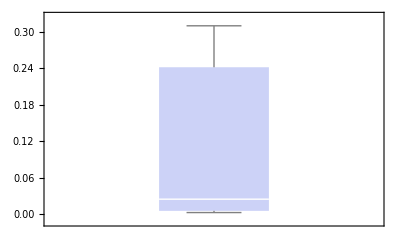

```mathematica
best = 1;
worst = 0;
sum = 0;
results={};
For[i = 1, i <= folds, i++,(*kod jednoho kola krossvalidace*)
 validationData = completeData[[1 + (i - 1)*vectorsInFold[[1]] ;; i*vectorsInFold[[1]]]];
 learnData = Drop[completeData, {1 + (i - 1)*vectorsInFold[[1]], i*vectorsInFold[[1]]}];
 validationDataIn = validationData[[All, 1 ;; 4]];
 validationDataOut = validationData[[All, 5 ;; 7]];
 learnDataIn = learnData[[All, 1 ;; 4]];
 learnDataOut = learnData[[All, 5 ;; 7]];
net=InitializeFeedForwardNet[inData,outData,{3,2},Neuron->Sigmoid];
 {net2, record} = NeuralFit[net, learnDataIn, learnDataOut, validationDataIn, validationDataOut, CriterionLog -> False, CriterionPlot -> False];
 current = Take[CriterionValidationValues /. record[[2]], -1];
 If[current[[1]] < best, best = current[[1]], best = best];
 If[current[[1]] > worst, worst = current[[1]], worst = worst];
sum = sum + current;
AppendTo[results,current[[1]]];
 Print[i ". fold = ", current[[1]]];
 ]
BoxWhiskerChart[results]
```

Vypsaly se výsledky sítě pro každý fold. Všimněte si, že jednotlivé výsledky sítě se značně liší a jsou závislé na konkrétním rozdělení dat a také na inicializaci sítě. Dále se zobrazil graf shrnující výsledky neuronové sítě, po najetí myší na graf se zobrazí podrobnosti.

Zobrazit výsledky křížové validace je možné také takto.

```mathematica
" = průměrný výsledek" sum[[1]]/folds
" = nejlepší výsledek" best
" = nejhorší výsledek" worst
```

0.0900545  = průměrný výsledek

0.00307601  = nejlepší výsledek

0.309673  = nejhorší výsledek

Pokud bychom nepoužili křížovou validaci a místo ní použili jak jedno konkrétní rozdělení dat, byly by naše informace o výkonu neuronové sítě značně nepřesné.

## Křížová validace vlastní sítě

Zde si můžete nechat provést křížovou validaci vlastní sítě s vlastními daty.

```mathematica
yourNet=InitializeFeedForwardNet[inData,outData,{3,2},Neuron->Sigmoid];(*Vaše dopředná nebo RBF síť*)
yourInData = inData;(*Vaše předzpracovaná vstupní data*)
yourOutData = outData;(*Vaše předzpracovaná výstupní data*)
yourFolds = folds;(*Váš počet foldů*)
```

Následující blok spusťte pro vyhodnocení vlastní sítě.

. fold = 0.0978016

2 . fold = 0.0090159

3 . fold = 0.216576

4 . fold = 0.00790153

5 . fold = 0.00714572

6 . fold = 0.258429

7 . fold = 0.0437423

8 . fold = 0.259688

9 . fold = 0.018088

10 . fold = 0.0113425

11 . fold = 0.0206056

12 . fold = 0.0441929

13 . fold = 0.240892

14 . fold = 0.140184

15 . fold = 0.280981

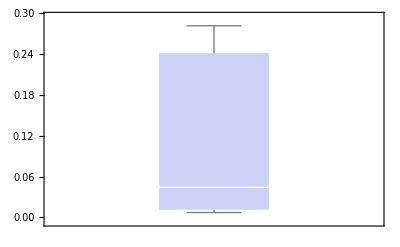

```mathematica
Off[NeuralFit::StoppedSearch];
yourVectors = Take[Dimensions[yourInData], 1];
inDataDimensions=Take[Dimensions[yourInData],-1];
outDataDimensions=Take[Dimensions[yourOutData],-1];
yourVectorsInFold = IntegerPart[yourVectors/yourFolds];
yourCompleteData = Join[yourInData, yourOutData, 2];
yourCompleteData = RandomSample[yourCompleteData];
yourBest = 1;
yourWorst = 0;
yourSum = 0;
yourResults={};
For[i = 1, i <= yourFolds, i++,(*kod jednoho kola krossvalidace*)
 yourValidationData = yourCompleteData[[1 + (i - 1)*yourVectorsInFold[[1]] ;; i*yourVectorsInFold[[1]]]];
 yourLearnData = Drop[yourCompleteData, {1 + (i - 1)*yourVectorsInFold[[1]], i*yourVectorsInFold[[1]]}];
 yourValidationDataIn = yourValidationData[[All, 1 ;; inDataDimensions[[1]]]]; yourValidationDataOut = yourValidationData[[All, inDataDimensions[[1]]+1 ;; inDataDimensions[[1]]+outDataDimensions[[1]]]];
 yourLearnDataIn = yourLearnData[[All, 1 ;; inDataDimensions[[1]]]];
 yourLearnDataOut = yourLearnData[[All, inDataDimensions[[1]]+1 ;; inDataDimensions[[1]]+outDataDimensions[[1]]]];
 {net2, record} = NeuralFit[yourNet, yourLearnDataIn, yourLearnDataOut, yourValidationDataIn, yourValidationDataOut, CriterionLog -> False, CriterionPlot -> False];
 current = Take[CriterionValidationValues /. record[[2]], -1];
 If[current[[1]] < yourBest, yourBest = current[[1]], yourBest = yourBest];
 If[current[[1]] > yourWorst, yourWorst = current[[1]], yourWorst = yourWorst];
 yourSum = yourSum + current;
AppendTo[yourResults,current[[1]]];
 Print[i ". fold = ", current[[1]]];
 ]
BoxWhiskerChart[yourResults]
```

Alternativní zobrazení výsledků:

```mathematica
" = průměrný výsledek" (yourSum/yourFolds)[[1]]
" = nejlepší výsledek" yourBest
" = nejhorší výsledek" yourWorst
```

0.110439  = průměrný výsledek

0.00714572  = nejlepší výsledek

0.280981  = nejhorší výsledek

## Prohlášení

Tento text je vypracován jako součást bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.